```mathematica
AlphaMin=0.00;
AlphaMax=1.00;
AlphaInterval=0.05;
gfacMin=1.00;
gfacMax=1.00;
gfacInterval=0.25;
nbasMin=14;
nbasMax=14;
nbasInterval=2;
noccMin=1;
noccMax=1;
noccInterval=1;
c1Min=0.00;
c1Max=1.00;
c1Interval=0.05;
omegaMin=2;
omegaMax=23;
omegaInterval=1;
Table[
Table[
Table[
Table[
Table[
Table[
Table[
res[gfac][nbas][nocc][omega][alpha][c0][c1]= ReadList["/home/grining/Dropbox/drake-mpfun/python/results/nocc="<>ToString[nocc]<>"nbas="<>ToString[nbas]<>"omega="<>ToString[omega]<>"gfac="<>ToString[NumberForm[gfac, {3,2}]]<>"alpha="<>ToString[NumberForm[alpha, {2,2}]]<>"c0="<>ToString[NumberForm[c0, {2,2}]]<>"c1="<>ToString[NumberForm[c1, {2,2}]]<>".out_FCCD"][[1]]
,{gfac, gfacMin, gfacMax,gfacInterval}];
,{nbas, nbasMin,nbasMax,nbasInterval}];
,{nocc, noccMin,noccMax,noccInterval}];
,{omega,omegaMin,omegaMax,omegaInterval}];
,{alpha,AlphaMin,AlphaMax,AlphaInterval}];
,{c1,c1Min,c1Max,c1Interval}];
,{c0,{1.00}}];
```

```mathematica
Table[
Table[
Res[alpha][c1]=Table[
res[1.00][14][1][omega][alpha][1.00][c1]
,{omega,omegaMin,omegaMax,omegaInterval}];
,{alpha,AlphaMin,AlphaMax,AlphaInterval}];
,{c1,c1Min,c1Max,c1Interval}];
```

```mathematica
Table[
Table[plotc1[alpha][omega]=Table[res[1.00][14][1][omega][alpha][1.00][c1],{c1,c1Min,c1Max,c1Interval}];
,{alpha,AlphaMin,AlphaMax,AlphaInterval}];
,{omega,omegaMin,omegaMax,omegaInterval}];
```

```mathematica
Table[
Table[plotalpha[c1][omega]=Table[res[1.00][14][1][omega][alpha][1.00][c1],{alpha,AlphaMin,AlphaMax,AlphaInterval}];
,{c1,c1Min,c1Max,c1Interval}];
,{omega,omegaMin,omegaMax,omegaInterval}];
```

```mathematica
plotalpha[0.05][10]
```

{1.306992947330022523636401173878201721609,1.306980235932159420853696738555327074668,1.306969726444994086109370907189807830749,1.306956569316934070634599605857559941142,1.306952735746885964110203677906256711506,1.307066284630317705155884954633486753195,1.307678653842256409722627166504683613067,1.309415624543539810276419446727743462547,1.312232250675603172622660641435792522409,1.314906343596528548858513006112318992503,1.316592838732059989801715430127670178173,1.3174106248061087302152980880359870548,1.317720825336288752203422934280906145126,1.317772546090990941605281731497865275657,1.317698114546269619619360661002762940687,1.317563506028045490104380150341565608332,1.317401604939532415028769255761849128454,1.317229097214219948078498656199108496169,1.317054598765099469996879141277970234432,1.316882591531305760344255155669028818224,1.316715380760110346956222770232312207292}

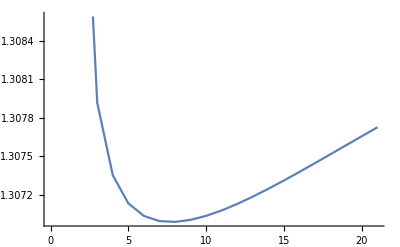
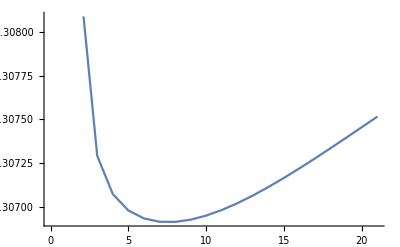
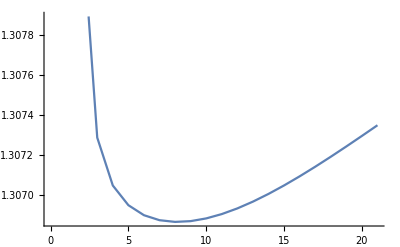
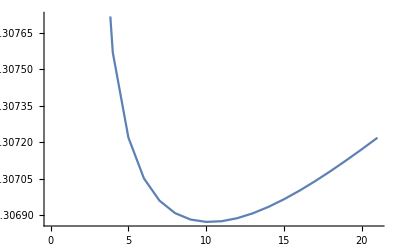
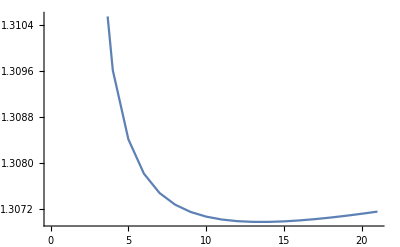
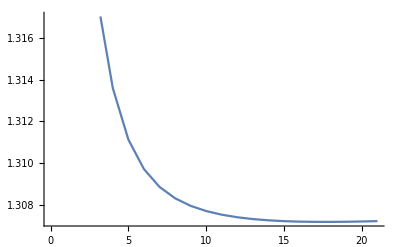
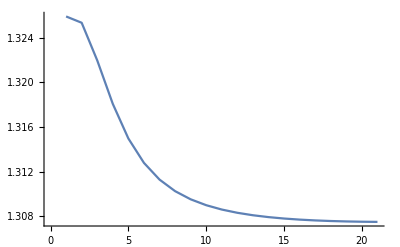
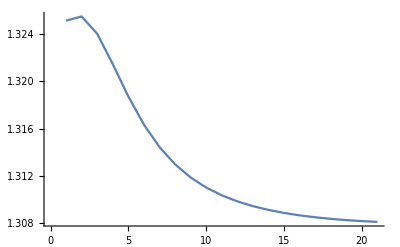

```mathematica
Table[ListLinePlot[plotc1[alpha][5]],{alpha,AlphaMin,AlphaMax,AlphaInterval}]
```

```mathematica
ListLinePlot[plotc1[0.00][5]]
```

-Graphics-